```mathematica
(*This will do the heat equation in 1D*)
alpha = 0.01;
sol = NDSolveValue[{{D[u1[x,t],t]==alpha*D[u1[x,t],{x,2}]},{u1[x,0]==-5*x*(x-1)},{u1[0,t]==0},{u1[1,t]==0}},u1,{x,0,1},{t,0,10}]
```

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
Manipulate[Plot[{k*x(x-1),0*x+10},{x,0,1}],{k,-20,5}]
```

```mathematica
Manipulate[Plot[{Evaluate[u1[x,t]/.sol],0*x+1.3},{x,0,1}],{t,0,10}]
```

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(*This will do the heat equation in 2D*)
```

```mathematica
alpha2 = 0.003;
sol2 = NDSolve[{{D[u2[x,y,t],t]==alpha2*(D[u2[x,y,t],{x,2}]+D[u2[x,y,t],{y,2}])},{u2[x,y,0]==10*x*(x-1)*y*(y-1)},{u2[0,y,t]==0},{u2[1,y,t]==0},{u2[x,0,t]==0},{u2[x,1,t]==0}},u2,{x,0,1},{y,0,1},{t,0,20}]
```

{{u2→InterpolatingFunction[{{0., 1.}, {0., 1.}, {0., 20.}}, <>]}}

```mathematica
Plot3D[{10*x*(x-1)*y*(y-1),0*x*y},{x,-1,2},{y,-1,2}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[{Evaluate[u2[x,y,t]/.sol2],{0*x*y+0.7}},{x,0,1},{y,0,1}],{t,0,20}]
```

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(*Goal is to make PDE over the following mesh*)
```

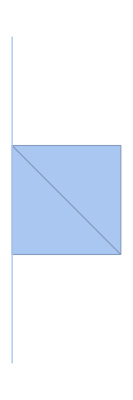

```mathematica
meshMixed = MeshRegion[ {{0,0},{0,1},{0,2},{0,3},{1,1},{1,2}}, {Line[{1,4}],Simplex[{2,3,5}],Simplex[{3,5,6}]}]
```

```mathematica
(* New boundary condition will be something like v[1,y,t]==Evalutate[u1[x,y,t]/.sol]*)
```

```mathematica
Plot3D[Evaluate[u1[x,0]/.sol]*(1-y),{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[Evaluate[u1[x,t]/.sol]*(1-y),{x,0,1},{y,0,1}],{t,0,20}]
```

```mathematica
sol3 = NDSolve[{{D[u3[x,y,t],t]==alpha2*(D[u3[x,y,t],{x,2}]+D[u3[x,y,t],{y,2}])},{u3[x,y,0]==Evaluate[u1[x,0]/.sol]*(1-y)},{u3[0,y,t]==0},{u3[1,y,t]==0},{u3[x,0,t]==Evaluate[u1[x,t]/.sol]},{u3[x,1,t]==0}},u3,{x,0,1},{y,0,1},{t,0,20}]
```

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}},«27»,{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}} is not a rectangular tensor with dimensions {29,15}.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

Set::take: Cannot take positions 1 through 3 in Abs[«1»].

Set::take: Cannot take positions -3 through -1 in Abs[«1»].

Set::take: Cannot take positions 1 through 3 in Abs[«1»].

General::stop: Further output of Set::take will be suppressed during this calculation.

```mathematica
sol3 = NDSolve[{{D[u3[x,y,t],t]==alpha2*(D[u3[x,y,t],{x,2}]+D[u3[x,y,t],{y,2}])},{u3[x,1,t]==0},{u3[0,y,t]==0},{u3[1,y,t]==0}},u3,{x,0,1},{y,0,1},{t,0,20}]
```

NDSolve::femcnmd: The PDE coefficient {{-alpha2,0,0},{0,-alpha2,0},{0,0,0}} does not evaluate to a numeric matrix of dimensions {3,3} at the coordinate {0.,0.,0.}.

NDSolve[{{u3^(0,0,1)[x,y,t]==alpha2 (u3^(0,2,0)[x,y,t]+u3^(2,0,0)[x,y,t])},{u3[x,1,t]==0},{u3[0,y,t]==0},{u3[1,y,t]==0}},u3,{x,0,1},{y,0,1},{t,0,20}]

```mathematica
sol[0.3,0]
```

1.05

```mathematica
Evaluate[u1[0.4,0.3]/.sol]*2
```

{2.34}